Лабораторная работа №5

```mathematica
sys1 = {x^2-y^2-15 == 0,x*y+4 == 0};
```

```mathematica
sys2 = {x^2+y^2+x+y-8 == 0,x^2+y^2+x*y-7 == 0};
```

```mathematica
Solve[sys1, {x, y}]
```

{{x→-4,y→1},{x→-ⅈ,y→-4 ⅈ},{x→ⅈ,y→4 ⅈ},{x→4,y→-1}}

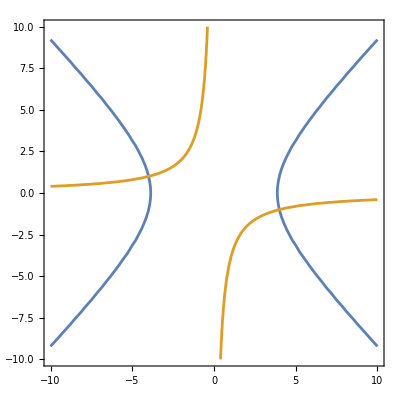

```mathematica
graph1 = ContourPlot[{x^2-y^2-15 == 0,x*y+4 == 0}, {x, -10, 10}, {y, -10, 10}, Axes -> True]
```

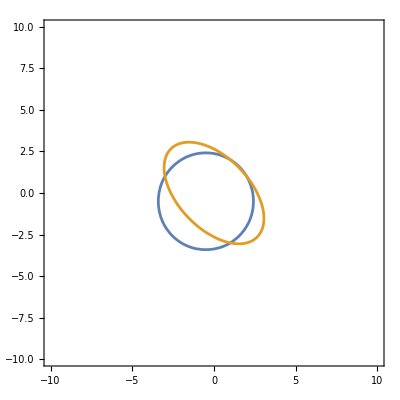

```mathematica
graph2 = ContourPlot[{x^2+y^2+x+y-8 == 0,x^2+y^2+x*y-7 == 0}, {x, -10, 10}, {y, -10, 10}, Axes -> True]
```

10

10

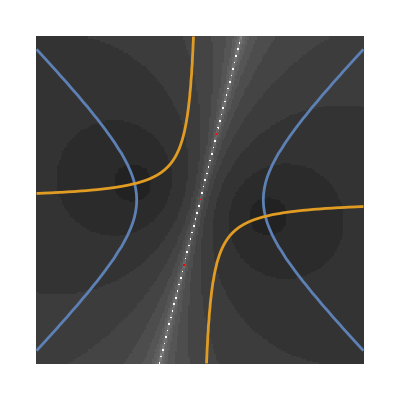

```mathematica
data=Import["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Методы вычислений\\Лабы\\code_lab5\\data.txt","table"];
xR=data[[1]][[1]]
yR=data[[1]][[2]]
n=data[[1]][[3]];
hx=2xR/n;
hy=2yR/n;
data=Drop[data, 1];
color[x_]:=If[x==0,RGBColor[1,0,0],RGBColor[x/30,x/30,x/30]];
Show[Graphics[Table[{color@data[[i]][[j]],Rectangle[{-xR+hx*(j-1),-yR+hy*(i-1)},{-xR+hx*j,-yR+hy*i}]},{i,1,n},{j,1,n}],PlotRange->{{-xR,xR},{-yR,yR}}, AspectRatio->Automatic], graph1]
```

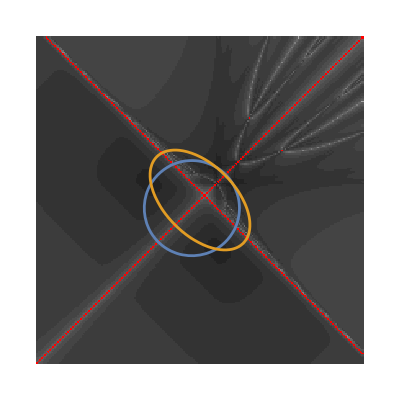

```mathematica
data=Import["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Методы вычислений\\Лабы\\code_lab5\\sys21.txt","table"];
xR=data[[1]][[1]];
yR=data[[1]][[2]];
n=data[[1]][[3]];
hx=2xR/n;
hy=2yR/n;
data=Drop[data, 1];
color[x_]:=If[x==0,RGBColor[1,0,0],RGBColor[x/30,x/30,x/30]];
Show[Graphics[Table[{color@data[[i]][[j]],Rectangle[{-xR+hx*(j-1),-yR+hy*(i-1)},{-xR+hx*j,-yR+hy*i}]},{i,1,n},{j,1,n}],PlotRange->{{-xR,xR},{-yR,yR}}, AspectRatio->Automatic], graph2]
```

10

10

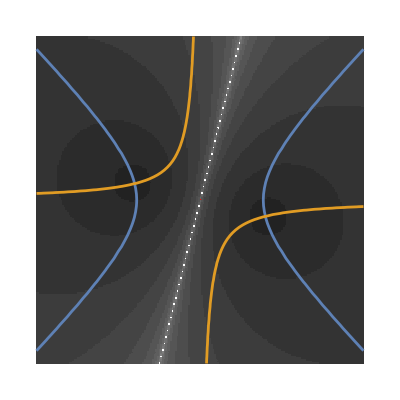

```mathematica
data=Import["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Методы вычислений\\Лабы\\code_lab5\\data.txt","table"];
xR=data[[1]][[1]]
yR=data[[1]][[2]]
n=data[[1]][[3]];
hx=2xR/n;
hy=2yR/n;
data=Drop[data, 1];
color[x_]:=If[x==0,RGBColor[1,0,0],RGBColor[x/30,x/30,x/30]];
Show[Graphics[Table[{color@data[[i]][[j]],Rectangle[{-xR+hx*(j-1),-yR+hy*(i-1)},{-xR+hx*j,-yR+hy*i}]},{i,1,n},{j,1,n}],PlotRange->{{-xR,xR},{-yR,yR}}, AspectRatio->Automatic], graph1]
```

10

10

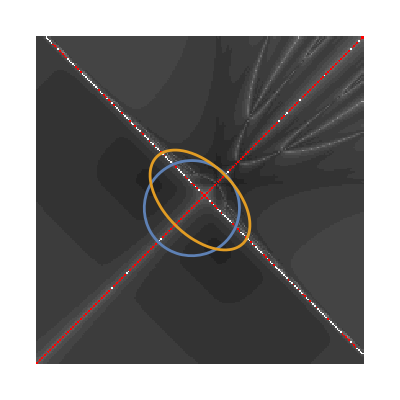

```mathematica
data=Import["C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Методы вычислений\\Лабы\\code_lab5\\sys22.txt","table"];
xR=data[[1]][[1]]
yR=data[[1]][[2]]
n=data[[1]][[3]];
hx=2xR/n;
hy=2yR/n;
data=Drop[data, 1];
color[x_]:=If[x==0,RGBColor[1,0,0],RGBColor[x/30,x/30,x/30]];
Show[Graphics[Table[{color@data[[i]][[j]],Rectangle[{-xR+hx*(j-1),-yR+hy*(i-1)},{-xR+hx*j,-yR+hy*i}]},{i,1,n},{j,1,n}],PlotRange->{{-xR,xR},{-yR,yR}}, AspectRatio->Automatic], graph2]
```